## Installations

### Initializations

```mathematica
Clear["Global`*"]
Needs["SymbolicC`"];
targetDir=NotebookDirectory[];
SetDirectory[targetDir];
```

### Install Packages: DoublePendulum.

```mathematica
MyPackageDirectory=ToFileName[{ParentDirectory[ParentDirectory[]],"Packages"}]
```

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/2-Atala/1-IRK Kodeak/4-Artikulurako-I/41-C (Artikulurako inplementazioa 01-02-2017)/Packages/

```mathematica
Get["DoublePendulumNEW`",Path->MyPackageDirectory];
Get["MyFunctions`",Path->MyPackageDirectory];
```

### Plot Style

```mathematica
StyleQuad=Red;
StyleIdeal=Orange;
StyleMachine=Lighter[Blue,.6];
StyleClassic=Lighter[Gray,.6];
StyleHairer=Green;
StyleError=Lighter[Blue,.6];
StyleEstimation=Orange;
StyleHamT12=Directive[Dashed,Red];
MarkerQuad="○"; (*○  △    □*)
MarkerIdeal="▲"; (*●  ▲  ■*)
MarkerMachine="■";
```

## Filenames

### Paths

```mathematica
DataDirectory="Data/";
ImagesDirectory="Images/";
```

### Input Files

```mathematica
filey0=NotebookDirectory[]<>DataDirectory<>"Datay0.bin";
fileA=NotebookDirectory[]<>DataDirectory<>"outA.bin";
fileTerminal=NotebookDirectory[]<>DataDirectory<>"Output.bin";
```

### Output Files

```mathematica
esperiment="NCDP";
(* energy error*)
plot1=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"3A.pdf";
plot1b=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"3B.pdf";
plot11=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot11.pdf";

(* distribution of energy jumps*)
plot4=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"2A.pdf";
```

## Parameters (NCDP)

### Problem parameters and initial values.

```mathematica
prec=100;
neq=4;
g=98/10;
m1=1;m2=1;
l1=1;l2=1;

C1=-l1^2 (m1+m2);
C2=-l2^2 m2;
C3=-2 l1 l2 m2 ;
C4=-2 l1^2 l2^2 m1 m2-l1^2 l2^2 m2^2;
C5=-l1^2 l2^2 m2^2;
C6=g l1 (m1+m2);
C7= g l2 m2;

Q10=(11/10);
Q20=-(11/10);
P10=13873/5000;
P20=13873/5000;
u0={Q10,Q20,P10,P20};
u0D= N[{Q10,Q20,P10,P20}];
u0DD=SetPrecision[u0D,prec];
ee0 =u0 - u0DD;

preal=parameters={C1,C2,C3,C4,C5,C6,C7};
pint={0,0};
```

### Integration parameters.

```mathematica
t0=0.;tend=2.^(12) ;
h=2.^(-7);
sampling=2^(10);
```

```mathematica
codfun0=1; (*OdePendulum*)

ns= 6;
nstep=(tend-t0)/h;
nout=nstep/sampling
```

512.

### RKG parameters

```mathematica
neq=Length[u0];
prec=100;
HAM=DoublePendulumHamNEW;
HAM2=DoublePendulumHam3NEW;
ERR=ErrorPosition;
ERRFORTRAN=ErrorPositionFortran;
```

## Import (math execution)

```mathematica
Now
```

Tue 18 Apr 2017 20:39:50GMT+2.

```mathematica
nstat=10;
```

### Parameters

```mathematica
noutA=Round[nout]+1;
step=1;
dd1= (2neq+1);
dd2= (3neq+1);
dd3=neq+1;
```

### Import

```mathematica
outA=SetPrecision[ArrayReshape[BinaryReadList[fileA,"Real64"],{nstat,noutA,dd1}],prec];
tpA=Flatten[Take[outA[[1]],All,{1,1}]];
tpA=Map[First,Partition[tpA,step]];
{Length[outA],Length[outA[[1]]]}
```

{10,513}

## Import (terminal execution)

```mathematica
Now
```

Sun 29 Jan 2017 11:01:11GMT+1.

```mathematica
nstat=1;
```

### Parameters

```mathematica
noutA=Round[nout]+1;
step=1;
dd1= (2neq+1);
dd2= (3neq+1);
dd3=neq+1;
```

### Import

```mathematica
outA=SetPrecision[ArrayReshape[BinaryReadList[fileTerminal,"Real64"],{nstat,noutA,dd1}],prec];
tpA=Flatten[Take[outA[[1]],All,{1,1}]];
tpA=Map[First,Partition[tpA,step]];
{Length[outA],Length[outA[[1]]]}
```

{1,513}

## Analisis-I

```mathematica
Now
```

Sun 29 Jan 2017 13:51:53GMT+1.

### Graphics-I (Energy): Plot1, Plot2

```mathematica
{MeanHamA,DesvHamA}=FunEnergy[outA, nstat,noutA,HAM, preal,neq,prec,step] ;
```

```mathematica
eskala=10^(15);
MeanHamAdata = Transpose[{tpA,MeanHamA*eskala}];
DesvHamAdata = Transpose[{tpA,DesvHamA*eskala}];
```

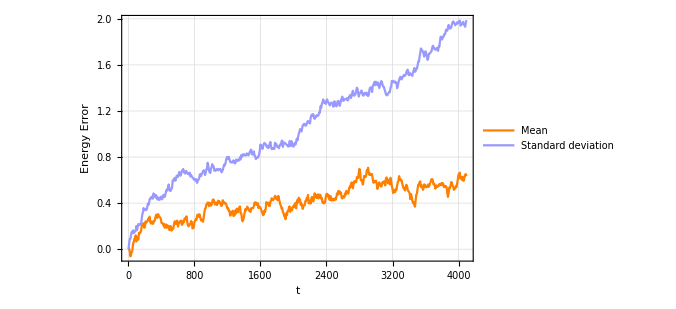

```mathematica
plot=ListPlot[{MeanHamAdata,DesvHamAdata},AxesLabel->{"t","Energia"},Joined->True,
PlotRange->All,
PlotLegends->Placed[{"Mean","Standard deviation"},Below],
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleIdeal,StyleMachine},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Energy Error"},
LabelStyle->Directive[Black,Bold]
]
Export[plot1,Show[plot] ];
```

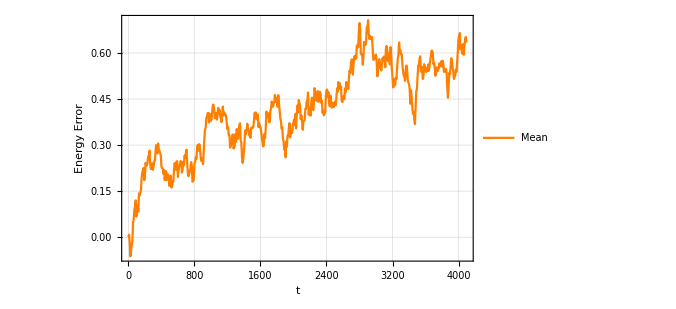

```mathematica
plot=ListPlot[{MeanHamAdata},AxesLabel->{"t","Energia"},Joined->True,
PlotRange->All,
PlotLegends->Placed[{"Mean"},Below],
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleIdeal},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Energy Error"},
LabelStyle->Directive[Black,Bold]
]
Export[plot1b,Show[plot] ];
```

### Graphics-I (Energy-2): Plot11.

```mathematica
maxnstat=100;
If[nstat<maxnstat,nstat0=nstat,nstat0=maxnstat];
```

```mathematica
AllHamerrA=FunAllEnergy[outA, nstat0,noutA,HAM, parameters,neq,prec,step] ;
```

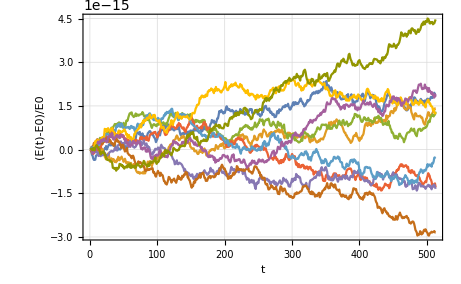

```mathematica
plot=ListPlot[Table[AllHamerrA[[i]],{i,nstat0}],AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
Export[plot11,Show[plot] ];
```

### Graphics-III (Histogram) : Plot4, Plot5

```mathematica
HamerrA=FunHamErrDif[outA,nstat,noutA,HAM, parameters,neq,prec,step] ;
```

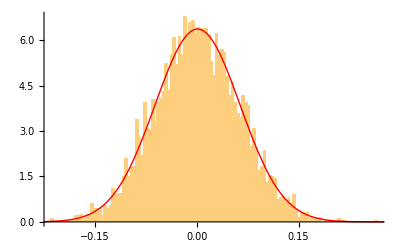

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/2-Atala/1-IRK Kodeak/4-Artikulurako-I/41-C (Artikulurako inplementazioa 01-02-2017)/Examples/NCDP/Images/NCDP2A.pdf

```mathematica
Hamerdif=HamerrA 10^15;
μ=Mean[Hamerdif];
σ=StandardDeviation[Hamerdif];
ir1=Histogram[Hamerdif,{σ/16},"PDF"];
ir2=Plot[PDF[NormalDistribution[μ,σ],x],{x,-16*σ,16*σ},PlotStyle->{Red,Thick},PlotRange->All,WorkingPrecision->prec];
Show[ir1,ir2]
Export[plot4,Show[ir1,ir2]]
```

```mathematica
MaxDE=Max[Abs[MeanHamA]]//N;
Hamerdif=Drop[MeanHamA ,1]-Drop[ MeanHamA,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
{MaxDE,μ,σ}
```

{7.06816×10^-16,1.23826×10^-18,2.40606×10^-17}